### Define the Parameters

```mathematica
ClearAll[c,λ,ω, k, TrfAmp, rfFre, Vpi, V0, Pmax, Pmin,ϵ]
```

ClearAll::ssym: k T rfAmp is not a symbol or a string.

```mathematica
c = 1;(*speed of light m/s*)
λ = 0.01;(*laser wavelength m*)
ω = 2π c/λ; (*angular frequency rad/s*)
k  = 2π/λ; (*wave number*)
T = 2π/ω;(*period*)
rfAmp = 0.5(*RF amplitude in V*)
rfAmp2 =0(*RF amplitude in V*)
rfFre = 0.6479;(*RF frequency in GHz*)
rfFre2= 0.7891;(*RF frequency in GHz*)
Vpi = 6; (*half-wave voltage*)
```

### Define equations

```mathematica
ClearAll[t,phase,x,p,v,Laser, Modulation]
```

```mathematica
Modulation[t_]:= rfAmp Cos[2π rfFre t]+rfAmp2 Cos[2π rfFre2 t];
subModulation1[t_]:= rfAmp Cos[2π rfFre t];
subModulation2[t_]:= rfAmp2 Cos[2π rfFre2 t];
phase[v_]:= v*π/Vpi;
Laser[phase_,t_]:= Exp[I( ω t+phase)];
```

### Plot the equations

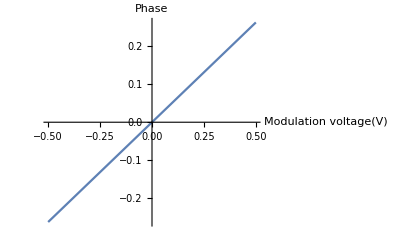

```mathematica
Plot[phase[v], {v,-rfAmp ,rfAmp }, AxesLabel->{ "Modulation voltage(V)","Phase"}]
```

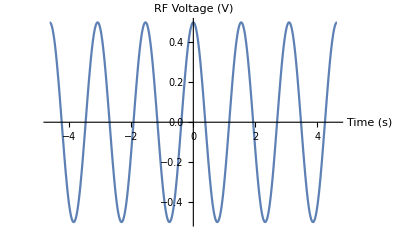

```mathematica
Plot[Modulation[t], {t,-3/rfFre,3/rfFre}, AxesLabel->{ "Time (s)","RF Voltage (V)"}]
```

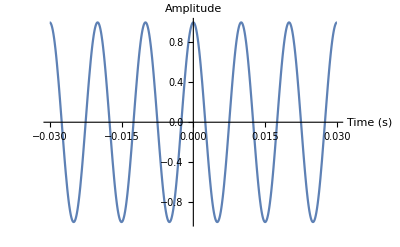

```mathematica
Plot[Re[Laser[0,t]/.{x->0}], {t,-3*2π/ω,3*2π/ω}, AxesLabel->{ "Time (s)","Amplitude"},PlotRange->All]
```

### Apply Modulation to Laser

```mathematica
ClearAll[dt,t,modulatedSignal]
```

```mathematica
t=Table[n,{n,0,10*10^1,1*10^-4}];(*Time array in seconds*)
dt=t[[2]]-t[[1]];(*Time step*)
modulatedSignal = Laser[phase[Modulation[t]],t]/.x->0;
submodulatedSignal1 = Laser[phase[subModulation1[t]],t]/.x->0;
submodulatedSignal2 = Laser[phase[subModulation2[t]],t]/.x->0;
laserSignal = Laser[0,t]/.x->0;
```

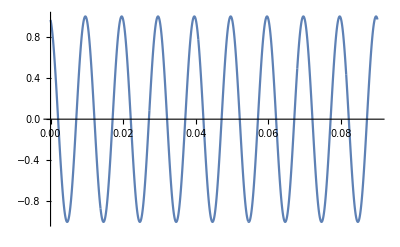

```mathematica
m = Laser[phase[Modulation[a]],a]/.x->0;
Plot[Re[m],{a,0,9*10^-2},PlotRange->All,PlotPoints->50000]
```

```mathematica
ListLinePlot[Transpose[{t,Re[modulatedSignal]}],PlotRange->{{0,5*10^-2},All},Frame->True,FrameLabel->{"Time (ns)","Amplitude"},PlotLabel->"Modulated Signal in Time Domain"]
```

-Graphics-

## Go to the Frequency Space

```mathematica
ClearAll[ftModulatedSignal,frequencies]
```

```mathematica
ftModulatedSignal=Fourier[modulatedSignal,FourierParameters->{-1,-1}];
```

```mathematica
ftLaser=Fourier[laserSignal,FourierParameters->{-1,-1}];
ftSideband1=Fourier[submodulatedSignal1,FourierParameters->{-1,-1}];
ftSideband2=Fourier[submodulatedSignal2,FourierParameters->{-1,-1}];

frequencies=Table[(n-1)/( dt Length[modulatedSignal]),{n,Length[modulatedSignal]}];
```

```mathematica
f[x_,μ_,FWHM_,height_]:=height/(1+((x-μ)/(FWHM/2))^2)

offset = 100 -23.4891 ;
center1=offset+22.1529;
center2=offset+23.4891;
center3=offset+24.1370;
FWHM=0.100;
height1=0.2;
height2=0.7;
height3=0.3;
A1 = f[frequencies,center1,FWHM,height1];
Ex = f[frequencies,center2,FWHM,height2];
A2 = f[frequencies,center3,FWHM,height3];
NV = A1+Ex+A2;
```

## Plot The Final Results

### Laser and NV Transitions

```mathematica
plotRange = 5;(*GHz*)
```

```mathematica
laser=ListLinePlot[Transpose[{frequencies,Abs[ftModulatedSignal]}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal in Frequency Domain",PlotStyle->Red];
nv =ListLinePlot[Transpose[{frequencies,NV}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal in Frequency Domain"];
Show[laser, nv,PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All}]
```

-Graphics-

### Laser and individual sideband

```mathematica
im1 = ListLinePlot[Transpose[{frequencies,Abs[ftLaser]}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal in Frequency Domain",PlotStyle->Black];
im2= ListLinePlot[Transpose[{frequencies,Abs[ftSideband1]}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal 1 in Frequency Domain",PlotStyle->Directive[Blue,Dashed]];
im3= ListLinePlot[Transpose[{frequencies,Abs[ftSideband2]}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal 2 in Frequency Domain",PlotStyle->Directive[Red,Dashed]];
Show[im2,im3,PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All}]
```

-Graphics-

```mathematica
center3-center2
```

0.6479

```mathematica
1.437-0.6479
```

0.7891

```mathematica
center2-center1
```

1.3362